```mathematica
f[x_,y_]:= 2 x^3 - 3x^2-6x y(x-y-1);
{sol, pts}=Reap[
NMinimize[f[x,y],{{x,-1,1},{y,-1,1}},  EvaluationMonitor:>Sow[{x,y}]]];
```

```mathematica
D[2 x^3 - 3x^2-6x y(x-y-1),{{x,y},2}]//Simplify
```

{{6 (-1+2 x-2 y),6-12 x+12 y},{6-12 x+12 y,12 x}}

```mathematica
Solve[x^2-18x-36==0,x]//N
```

{{x→-1.81665},{x→19.8167}}

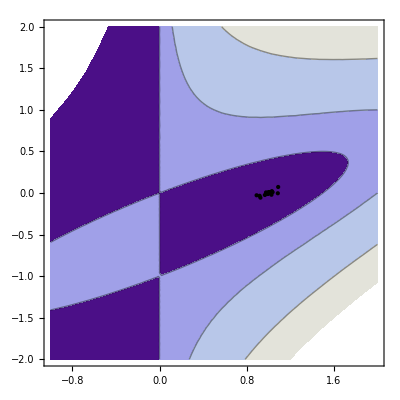

```mathematica
ContourPlot[f[x,y],{x,-1,2},{y,-2,2},
Epilog->Map[Point,Cases[First[pts],x_/;Abs[f@@x-First[sol]]≤.05]], Contours->4Range[0,10]^2]
```

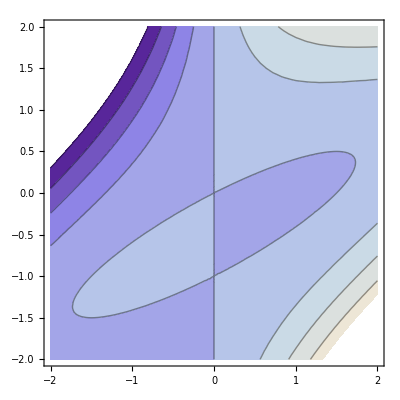

```mathematica
ContourPlot[(2 x^3-3 x^2-6 x y (x-y-1)),{x,-2,2},{y,-2,2}]
```

```mathematica
ColorFunction->(Hue[.6(1-#1)]&),
```